Suna Zekioglu

## Introduction to Calculating in Mathematica

## Some fundamentals

### Lists, Vectors, and Matrices

#### Basic Lists

Lists are essentially the arrays of Mathematica, and they’re pretty flexible. To evaluate this, press shift+return or shift+enter:

```mathematica
myList = {a,b,c,d,e} (*this is a comment and it doesn't get evaluated!*)
```

{a,b,c,d,e}

They start indexing from 1, not 0, and you can use negative indices to denote counting backwards from the end:

```mathematica
myList[[1]]
```

a

```mathematica
myList[[-2]]
```

d

```mathematica
First[myList]
```

a

```mathematica
Last[myList]
```

e

The zeroth entry tells you the head of the expression – in this case, List (we’ll see how this is useful later):

```mathematica
myList[[0]]
```

List

You can apply functions to each item in a list using /@

```mathematica
Exp/@myList
```

{ⅇ^a,ⅇ^b,ⅇ^c,ⅇ^d,ⅇ^e}

Nested lists are also useful (note how the semicolon suppresses the output of somePoints):

```mathematica
somePoints ={{x1,y1},{x2,y2},{x3,y3}};
```

```mathematica
xPoints = First/@somePoints
```

{x1,x2,x3}

```mathematica
yPoints = Last/@somePoints
```

{y1,y2,y3}

Other list functions that are useful (but there are plenty plenty more in the documentation):

```mathematica
Total[myList]
```

a+b+c+d+e

```mathematica
Append[myList,f]
```

{a,b,c,d,e,f}

```mathematica
Join[{a,b,c},{x,y,z}]
```

{a,b,c,x,y,z}

```mathematica
Flatten[{a,{b},{{{c,d}}},e}]
```

{a,b,c,d,e}

```mathematica
MemberQ[myList,a](*is 'a' in the list?*)
```

True

```mathematica
MemberQ[myList,q](*is 'q' in the list?*)
```

False

#### Vectors and Matrices

To enter a vector, just do a simple list of the components:

```mathematica
aVector = {x,y,z};
```

To enter a matrix, simply created a nested list of the rows. You can visualize what you’ve typed in by applying the function MatrixForm (but don’t try to use an expression in MatrixForm to do the calculations I’ve sketched out below):

```mathematica
aMatrix = {{a,b,c},{d,e,f},{g,h,i}};
```

```mathematica
MatrixForm[aMatrix]
```

(a | b | c
d | e | f
g | h | i)

Get components as matrix[[row]][[column]]

```mathematica
aMatrix[[1]][[2]]
```

b

There are several ways to apply a function in Mathematica that I’ll use fairly interchangeably throughout this notebook:

```mathematica
(*"postfix" form*)
```

```mathematica
aMatrix//MatrixForm
```

(a | b | c
d | e | f
g | h | i)

```mathematica
(*"prefix" form*)
```

```mathematica
MatrixForm@aMatrix
```

(a | b | c
d | e | f
g | h | i)

#### Matrix Multiplication

To do a dot product, use the . operator:

```mathematica
sampleDot = aVector.aVector
```

x^2+y^2+z^2

Similarly this works for matrix multiplication:

```mathematica
aMatrix.aVector
```

{a x+b y+c z,d x+e y+f z,g x+h y+i z}

```mathematica
aMatrix.aVector //MatrixForm
```

(a x+b y+c z
d x+e y+f z
g x+h y+i z)

#### Eigenvectors and Eigenvalues

Mathematica is pretty good at doing this for you. For some given matrix:

```mathematica
hamiltonian = {{E0,Δ},{Δ,E0}};
```

```mathematica
hamiltonian//Eigenvalues
```

{E0-Δ,E0+Δ}

```mathematica
hamiltonian//Eigenvectors
```

{{-1,1},{1,1}}

Note you'd need to normalize these yourself; we'll write a function to do this automatically later.

```mathematica
hamiltonian//Eigensystem
```

{{E0-Δ,E0+Δ},{{-1,1},{1,1}}}

Let’s check these results by testing that the matrix acting on its eigenvectors yields the eigenvalues provided:

```mathematica
{eigenvector1,eigenvector2} = hamiltonian//Eigenvectors;
```

```mathematica
{eigenvalue1,eigenvalue2} = hamiltonian//Eigenvalues;
```

```mathematica
hamiltonian.eigenvector1 == eigenvalue1*eigenvector1
```

True

```mathematica
hamiltonian.eigenvector2 == eigenvalue2*eigenvector2
```

True

#### Functions of Matrices

Easy to exponentiate a matrix; let’s try with one of the Pauli matrices. Capital I is the imaginary unit in Mathematica:

```mathematica
pauliX = {{0,1},{1,0}};
```

```mathematica
MatrixExp[I*θ*pauliX] //MatrixForm
```

(Cos[θ] | ⅈ Sin[θ]
ⅈ Sin[θ] | Cos[θ])

### Writing Functions

#### Basics

Mathematica isn’t fussy about declaring the types of objects a function can take/return. The basic syntax is:

```mathematica
functionName[argument1_,argument2_]:= argument1 + argument2
```

Can use this function on numerical values, symbolic arguments, or both!

```mathematica
functionName[1,4]
```

5

```mathematica
functionName[x,y]
```

x+y

```mathematica
functionName[z,2]
```

2+z

Functions can return multiple values in the form of a list {returnValue1, returnValue2, ...}:

```mathematica
polarsToCartesians[r_, θ_]:= {r*Cos[θ],r*Sin[θ]}
```

```mathematica
polarsToCartesians[1,π/4]
```

{1/(√2),1/(√2)}

```mathematica
polarsToCartesians[r,-θ]
```

{r Cos[θ],-r Sin[θ]}

#### Local Variables (Module)

Let’s say we wanted to write a more complicated function, where we have an intermediate value that will help in the calculation of the final answer. This value should be stored as a local variable using Module. The last quantity inside Module will automatically be returned by the function. Here’s an example that I’ll explain below:

```mathematica
perfectSquareQ[argument1_]:= Module[{localVariable1},
localVariable1 = Sqrt@argument1;
 IntegerQ@localVariable1]
```

```mathematica
perfectSquareQ[3]
```

False

```mathematica
perfectSquareQ[25]
```

True

This function wants to check if the argument is a perfect square (we could have written a much slicker version of this function without needing to use Module of course, but it can’t hurt to start with a simple example). First localVariable1 is declared to be a local variable within the scope of Module. It calculates the square root of the argument and stores this value in localVariable1. Then it checks if localVariable1 is an integer using a built-in Mathematica function IntegerQ, and returns this result. Once the function evaluation is complete, the value stored in localVariable1 is wiped. We can see this even more clearly by writing the modified function:

```mathematica
perfectSquareQmod[argument1_]:= Module[{localVariable1},
localVariable1 = Sqrt@argument1;
Print[localVariable1];
IntegerQ@localVariable1]
```

```mathematica
perfectSquareQmod[47]
```

√47

False

```mathematica
localVariable1
```

localVariable1

During evaluation of the function, printing localVariable1 returns a value, √47.  After evaluation, localVariable1 has no value assigned to it – hence why it shows up in blue, and not in black, like global variables that have been assigned a value:

```mathematica
globalVariable =Sqrt@47;
```

```mathematica
globalVariable
```

√47

#### Some slightly more interesting examples

Let’s write a function to normalize a vector. The syntax for the arguments given to the function below means that Mathematica will look inside the list passed to the function and use its first term as xComponent and its second term as yComponent.

```mathematica
normalizeIt[{xComponent_,yComponent_}]:= Module[{norm},
norm = Sqrt[xComponent*xComponent + yComponent*yComponent];
{xComponent,yComponent}/norm]
```

```mathematica
normalizeIt[{x,y}]
```

{x/(√(x^2+y^2)),y/(√(x^2+y^2))}

```mathematica
normalizeIt[{3,4}]
```

{3/5,4/5}

Can write an even neater (and more general to n-dimensions!) version of this function, of course, using the dot product we learned earlier:

```mathematica
normalizeItNew[vector_]:= vector/Sqrt[vector.vector]
```

```mathematica
normalizeItNew[{1,1,1}]
```

{1/(√3),1/(√3),1/(√3)}

Now let’s use this to create a function that finds the normalized eigenvectors of a matrix (note that in this example, I’ve gone ahead and initialized the local variable eigenvectors at the same time as declaring it):

```mathematica
getNormalizedEigenvectors[matrix_]:= Module[{eigenvectors = Eigenvectors@matrix},
normalizeItNew/@eigenvectors]
```

The syntax functionName /@ list applies the function to every element of the list individually (so to each eigenvector individually), and returns a list of those results.

```mathematica
getNormalizedEigenvectors@hamiltonian
```

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

### Loops and Other Structures

#### Conditionals

If statements are pretty standard. Let’s use an If statement to write a function that gets mad about the idea of complex numbers:

```mathematica
mySqrt[x_]:= If[x≥0,√x//N, "Error: enter a non-negative number"]
```

The function N is useful for when you just want a decimal and Mathematica spits out 328/45 or √70 instead.

```mathematica
mySqrt[10]
```

3.16228

```mathematica
mySqrt[-4]
```

Error: enter a non-negative number

#### Systems of Equations, Reduce, and (To)Rules

Be careful with equals signs: a single equals sign “=” is for assignment; “==” is for an equation (and remains symbolic until values are assigned to the variables on either side that allow Mathematica to determine if the equation is consistent); and “===” immediately tests whether the expressions on each side are identical.

```mathematica
a = 4 (*assignment*)
```

4

```mathematica
a
```

4

```mathematica
x == y (*an equation*)
```

x==y

```mathematica
(*note x is still unassigned:*)
```

```mathematica
x
```

x

```mathematica
2 == 3
```

False

```mathematica
x === y (*check identical*)
```

False

```mathematica
x===x (*check identical*)
```

True

And maybe I want to use “a” later and not have it evaluate to 4:

```mathematica
Clear[a]
```

To solve a system of equations, use Reduce. Reduce takes a set of equations, and then optionally list of variables to eliminate. It’s often useful to store the results in a list of rules that can be applied later:

```mathematica
solutionRules = ToRules@Reduce[{2a == y + x, 2c== x-y},{x,y}]
```

{x→a+c,y→a-c}

```mathematica
(*to apply rules, syntax is expression /. rules*)
```

```mathematica
(x^2 - y^2) /. solutionRules  //FullSimplify
```

4 a c

#### Table

In Mathematica, For loops aren’t really a thing; instead, use Table (or Do). Table has the same sort of action as a For loop, but it’s cleaner once you get used to it, and it stores the value obtained upon each iteration in a list for later use. Table and Do always end in a syntax that specifies what values to iterate over; below, i runs from 1 to 10, and units of 1 are assumed:

```mathematica
squares = Table[i^2,{i,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Let’s use Table to find the sum of the integers from 1 to 100 (obviously there’s better ways to do this, including in Mathematica, but hey, it’s an example). Initialize some variable to hold a running total. Then, allow the table to run over the integers in question, adding the next one to the total at every step. Finally, once Table has generated that list, ask for the final answer by grabbing the last element of the list “sums”:

```mathematica
total = 0;
sums = Table[total += i,{i,1,100}];
Last@sums
```

5050

We can see that the list generated by Table, sums, holds all the intermediate values of the calculation:

```mathematica
sums
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050}

You can also do intermediate calculations in a table. The last line before the loop variable declaration is what will be output to the list. Here’s an example that grabs the first few terms in the Taylor series of Exp[-x] around x = 0. The variable “sign” is an intermediate calculation; the table only saves sign*x^n/(n!).

```mathematica
expTerms = Table[sign = (-1)^n;
sign*x^n/(n!),{n,0,8}]
```

{1,-x,x^2/2,-x^3/6,x^4/24,-x^5/120,x^6/720,-x^7/5040,x^8/40320}

```mathematica
expansion = Total@expTerms
```

1-x+x^2/2-x^3/6+x^4/24-x^5/120+x^6/720-x^7/5040+x^8/40320

May as well check how good an approximation this was:

```mathematica
Exp[-0.1] - (expansion/.x-> 0.1)
```

-2.88658×10^-15

A table doesn’t have to run over some list of consecutive integers, either. You can instead loop over the elements of a list. I’m using Range to generate a sample list here:

```mathematica
xList = Range[10,15,0.5]
```

{10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.}

```mathematica
Table[x/2,{x, xList}] (*read this as looping over each element, locally named 'x',  in the list xList*)
```

{5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5}

The list elements iterated over don’t even need to be numbers.

#### Do

Do is the same as Table, except it doesn’t output anything (unlike Table, which outputs a list). This is good for when you don’t need the value at each step of a calculation, or if indeed you’re not even doing a calculation at every step! Here’s an example looking for the minimum value in some list of data:

```mathematica
findMinimum[data_]:= Module[{currentMin = First@data},
Do[If[point < currentMin,currentMin = point],{point, data}];
currentMin]
```

```mathematica
yValues = Table[RandomReal[],{i,1,10}]
```

{0.185894,0.0962669,0.785408,0.854364,0.509919,0.634889,0.482228,0.979755,0.389084,0.168776}

```mathematica
findMinimum[yValues]
```

0.0962669

We could’ve used Table for this task, but the output of the table would’ve looked weird and not be super useful:

```mathematica
findMinimumAlt[data_]:= Module[{currentMin = First@data,tab},
tab=Table[If[point < currentMin,currentMin = point],{point, data}];
Print@tab;
currentMin]
```

```mathematica
findMinimumAlt[yValues]
```

{Null,0.0962669,Null,Null,Null,Null,Null,Null,Null,Null}

0.0962669

Do is also fairly useful when you need to modify a pre-existing object at every step of a calculation. Here, let’s generate a n-terms Fibonacci sequence, non-recursively for a change. At every iteration in Do, add to the end of the list Fibonacci another element that’s the sum of the current last two terms:

```mathematica
fibonacciSequence[nTerms_]:= Module[{fibonacci = {0,1},n = nTerms - 2},Do[fibonacci = Append[fibonacci,fibonacci[[-1]]+fibonacci[[-2]]],{i,n}];
fibonacci]
```

```mathematica
fibonacciSequence[10]
```

{0,1,1,2,3,5,8,13,21,34}

### Other Useful Stuff

#### Very Basic Plots

```mathematica
f[x_]:=x^2 Sin[π x]
```

Really you just wanna look at the documentation for Plot every time you make one, and personalize from there.... this one doesn’t look great but this is the basic syntax for a passable plot:

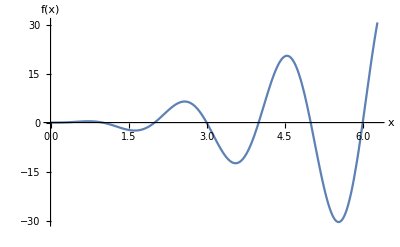

```mathematica
Plot[f[x],{x,0,2π},AxesLabel->{"x","f(x)"}]
```

For a scatter plot, nested list structure {{x1,y1},{x2,y2},...}

```mathematica
y[x_]:= x+2 x^2
```

```mathematica
scatterPlot = Table[{x,y[x]},{x,0,10}];
```

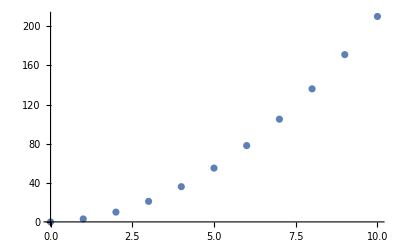

```mathematica
ListPlot[scatterPlot]
```

#### Simple ODE Solving

NDSolve takes arguments as follows:

```mathematica
(*NDSolve[{diffEquation, boundary conditions},nameOfFunctionToSolveFor,{domain for solution}]*)
```

```mathematica
approxCosine= NDSolve[{g''[x]+g[x]==0,g[0]==1,g'[0]==0},g,{x,0,4π}]
```

{{g→InterpolatingFunction[…]}}

It’s important not to use this solution outside the domain in which it was solved (in this case, from x = 0 to x = 4π)

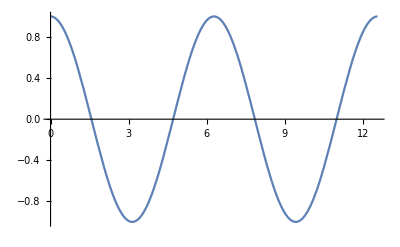

```mathematica
Plot[g[x]/.approxCosine,{x,0,4π}]
```

#### Integration

Mathematica can handle both symbolic and numerical integration. For symbolic, can do indefinite or definite integration:

```mathematica
Integrate[(Sin[2x])^2,x]
```

x/2-1/8 Sin[4 x]

```mathematica
Integrate[(Sin[2x])^2,{x,0,π}]
```

π/2

```mathematica
NIntegrate[Log[x]Sin[x],{x,π, 2π}]
```

-3.07884

## More advanced fun

### Pattern Matching

#### Rules and Basic Pattern Recognition

Mathematica is very good at this!! You can use rules to do all manner of things. The simplest thing we’ve already covered is just evaluating an expression:

```mathematica
(c+ 2)/.c-> 5
```

7

But we can also use them to do more complicated things. Let’s say we have objects with two arguments:

```mathematica
someObjects = {r[1,4],r[12,c],r[a,9b]};
```

And we want them to only have one argument instead by putting the arguments into a single list object. Try this:

```mathematica
someObjects/.r[a_,b_]:> r[{a,b}]
```

{r[{1,4}],r[{12,c}],r[{a,9 b}]}

The underscores after a_ and b_ denote that they can be anything, but in r[a_,b_], the header must really be ‘r’, so this doesn’t work:

```mathematica
c[1,4]/.r[a_,b_]:> r[{a,b}]
```

c[1,4]

This syntax looks for precisely two arguments, so the following has no effect:

```mathematica
r[1,3,2]/.r[a_,b_]:> r[{a,b}]
```

r[1,3,2]

#### More Pattern Stuff

Three underscores after the pattern argument, like a___, looks for any number of arguments, including zero (two underscores looks for any non-zero number of arguments, as we’ll see below). The following rule converts the arguments to a list, regardless of the number of arguments.

```mathematica
r[1,3,2]/.r[a___]:> {a}
```

{1,3,2}

```mathematica
r[1,a]/.r[a___]:> {a}
```

{1,a}

```mathematica
r[1,3,2]/.r[a___]:> Length[{a}] (*counts the number of arguments*)
```

3

```mathematica
r[1]/.r[a___]:> Length[{a}]
```

1

```mathematica
r[]/.r[a___]:> Length[{a}]
```

0

Two underscores behaves the same unless there are no arguments:

```mathematica
r[1,3,2]/.r[a__]:> {a}
```

{1,3,2}

```mathematica
r[]/.r[a__]:> Length[{a}] (*no effect*)
```

r[]

### Functions are Flexible

#### Pure Functions

```mathematica
list = a/@Range@5
```

{a[1],a[2],a[3],a[4],a[5]}

Here’s pure function syntax at its most basic, just printing a list out:

```mathematica
#&/@list
```

{a[1],a[2],a[3],a[4],a[5]}

# represents an element of the list, and &/@ tells it to run through all the elements # in “list.” Let’s say we wanted to get just the indices of this list:

```mathematica
First@#&/@list
```

{1,2,3,4,5}

Or just the headers:

```mathematica
Head@#&/@list
```

{a,a,a,a,a}

Of course, we could’ve done this all without pure functions, so let’s try a slightly more interesting example. Let’s say we have a whole list of coefficients that should all equal zero. As an example, let’s consider the vector equation: 
	v⃗ + w⃗ = OverVector[0]

```mathematica
vVector = v/@{x,y,z}
```

{v[x],v[y],v[z]}

```mathematica
wVector =vVector/.v[a_]:> w[a]
```

{w[x],w[y],w[z]}

```mathematica
total = vVector+wVector
```

{v[x]+w[x],v[y]+w[y],v[z]+w[z]}

To set up a system of equations to solve for total being the zero vector, let’s use pure function notation to grab each element/component of total, then set it equal to zero:

```mathematica
#==0 &/@total
```

{v[x]+w[x]==0,v[y]+w[y]==0,v[z]+w[z]==0}

#### Map

I’ve actually been using Map, or ‘/@’ a lot already. Just allows you to apply a function to each element of a list individually, rather than to the whole list (which is what @ would do)

```mathematica
functionName /@ {element1,element2,element3}
```

{functionName[element1],functionName[element2],functionName[element3]}

```mathematica
Clear[f]
```

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

You don’t need to actually have a defined function, so it’s a nice way to label things:

```mathematica
k/@Range@4
```

{k[1],k[2],k[3],k[4]}

#### Thread

Thread does this:

```mathematica
ClearAll[x,y,z]
```

```mathematica
Thread[{x,y,z}-> {1,2,3}]
```

{x→1,y→2,z→3}

I find this super useful when trying to run over a bunch of permutations:

```mathematica
perms3 = Permutations[k/@Range@3]
```

{{k[1],k[2],k[3]},{k[1],k[3],k[2]},{k[2],k[1],k[3]},{k[2],k[3],k[1]},{k[3],k[1],k[2]},{k[3],k[2],k[1]}}

```mathematica
allPossiblePermutationRules = Thread[(k/@Range@3)-> #]&/@perms3
```

{{k[1]→k[1],k[2]→k[2],k[3]→k[3]},{k[1]→k[1],k[2]→k[3],k[3]→k[2]},{k[1]→k[2],k[2]→k[1],k[3]→k[3]},{k[1]→k[2],k[2]→k[3],k[3]→k[1]},{k[1]→k[3],k[2]→k[1],k[3]→k[2]},{k[1]→k[3],k[2]→k[2],k[3]→k[1]}}

So now we have a list of lists of rules, with each set of rules permuting the k labels in a given way.

#### Apply

Apply (@@) replaces the head of an expression with something else:

```mathematica
New@@Old[a]
```

New[a]

This is useful in conjunction with the knowledge that Mathematica stores even the most basic expressions as a header and arguments. We can always see how Mathematica thinks about an expression by using FullForm:

```mathematica
(a+ b+c) //FullForm
```

Plus[a,b,c]

```mathematica
a*b/c //FullForm
```

Times[a,b,Power[c,-1]]

So, for a+b+c , if we wanted a list of these things instead of the sum of them, we could simply tell Mathematica to change Plus to List:

```mathematica
Plus[a,b,c]/.Plus->  List
```

{a,b,c}

But we can also achieve this more neatly use apply:

```mathematica
List@@Plus[a,b,c]
```

{a,b,c}

```mathematica
List@@(a+b+c)
```

{a,b,c}

```mathematica
Times@@{a,b,c}
```

a b c

We can of course use apply with undefined functions:

```mathematica
dotProduct@@{a,b}
```

dotProduct[a,b]

```mathematica
(*note this is different from:*)
dotProduct@{a,b}
```

dotProduct[{a,b}]

We can also use a variation of apply that affects each element in a list (@@@):

```mathematica
tryApply@@{a+b,c+d,e+f}
```

tryApply[a+b,c+d,e+f]

```mathematica
tryApply@@@{a+b,c+d,e+f}
```

{tryApply[a,b],tryApply[c,d],tryApply[e,f]}

Using @@@ tryApply replaces the head of each element of the list, which in this case was Plus:

```mathematica
{a+b,c+d,e+f}//FullForm
```

List[Plus[a,b],Plus[c,d],Plus[e,f]]

Whereas using @@ replaces the head of the list, List, with tryApply.

### Constraining Expressions

#### Coefficient Arrays

Coefficient arrays are nice for solving constraint equations. The basic idea is that they take some expression and some set of independent basis elements and find all combinations of coefficients appearing in front of independent combinations of basis elements. Here’s an example with a quartic polynomial in x and y:

```mathematica
variables = Power[x,#]*Power[y,4-#]&/@Range[0,4]
```

{y^4,x y^3,x^2 y^2,x^3 y,x^4}

```mathematica
polynomial =  (a/@Range@Length@variables).variables
```

y^4 a[1]+x y^3 a[2]+x^2 y^2 a[3]+x^3 y a[4]+x^4 a[5]

```mathematica
CoefficientArrays[polynomial,{x,y}]
```

{0,SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

Each ‘SpareArray’ corresponds to a different total number of the basis elements ‘x’ and ‘y’ appearing in each term. Think of the first element just being the coefficient of x^0 y^0, the second element a 1-by-2 matrix of the coefficients of x^1 y^0 and x^0 y^1, then the next one is a 2-by-2 of quadratic terms x^2 y^0, x^1 y^1, x^0 y^2, etc. We only have quartic terms, so let’s grab the last one:

```mathematica
Normal@Last@CoefficientArrays[polynomial,{x,y}]
```

{{{{a[5],a[4]},{0,a[3]}},{{0,0},{0,a[2]}}},{{{0,0},{0,0}},{{0,0},{0,a[1]}}}}

This can be hard to read, so use the following syntax to see the elements:

```mathematica
Last/@ArrayRules@Last@CoefficientArrays[polynomial,{x,y}]
```

{a[3],a[5],a[4],a[2],a[1],0}

One nice application of CoefficientArrays is for when you’d like to constrain an expression. Let’s say we wanted our polynomial to be even under x → –x. This constraint is represented by:

```mathematica
difference =polynomial - (polynomial/.x-> -x)
```

2 x y^3 a[2]+2 x^3 y a[4]

```mathematica
difference == 0
```

2 x y^3 a[2]+2 x^3 y a[4]==0

It’s obvious that the solution to this simple example is a[2] = a[4] = 0, but just letting Solve or Reduce go to town on this equation doesn’t give the desired results, since it doesn’t know that x and y are independent variables, so it gives a whole slew of nonsense solutions in addition to the one we’d like:

```mathematica
Reduce[difference == 0]
```

(a[4]==0&&a[2]==0)||(a[4]≠0&&(x==-(ⅈ y √a[2])/(√a[4])||x==(ⅈ y √a[2])/(√a[4])))||(a[4]==0&&a[2]≠0&&y==0)||x==0||y==0

```mathematica
Solve[difference == 0]
```

{{x→0},{y→0},{a[4]→-(y^2 a[2])/x^2},{x→0,y→0},{x→0,a[2]→0}}

Since we know the solution has to hold for any x and y, let’s use CoefficientArrays to get the coefficients of these independent x and y type terms:

```mathematica
Last/@ArrayRules@Last@CoefficientArrays[difference,{x,y}]
```

{2 a[4],2 a[2],0}

And set them each (since they accompany distinct independent basis elements) to zero:

```mathematica
#==0 &/@ Last/@ArrayRules@Last@CoefficientArrays[difference,{x,y}]
```

{2 a[4]==0,2 a[2]==0,True}

```mathematica
makeEven = ToRules@Reduce[#==0 &/@ Last/@ArrayRules@Last@CoefficientArrays[difference,{x,y}]]
```

{a[4]→0,a[2]→0}

```mathematica
evenPolynomial = polynomial/.makeEven
```

y^4 a[1]+x^2 y^2 a[3]+x^4 a[5]

#### Sow & Reap

Let’s say you have some expression full of coefficients a[i_], and you constrain the expression in some manner, and you want to know what coefficients a[i_] are left. There’s a nice way to do this! Continuing our polynomial example, let’s imagine for a moment this expression were really long and reading off the coefficients by eye would be really tedious. What Sow & Reap do here is look for the pattern a[some index], and every time they find that, add it to some list. The rest of the syntax just cleans up the output of reap to give a list of the unique coefficients a[i_]:

```mathematica
evenPolynomial
```

y^4 a[1]+x^2 y^2 a[3]+x^4 a[5]

```mathematica
remainingCoefficients = evenPolynomial/.a[i_]:> Sow[a[i]]//Reap//Last//Flatten//Union
```

{a[1],a[3],a[5]}

thanks, sow & reap!

Can also package this into a useful function:

```mathematica
extractType[data_,head_]:= data/.head[a___]:> Sow@head@a//Reap//Last//Flatten
```

And also introduce the notion of ‘infix’ notation for applying a function:

```mathematica
evenPolynomial~extractType~a
```

{a[1],a[3],a[5]}

## Amplitudes-y stuff

### Useful for functional ansatze

#### Undefined Functions with Properties

You can use functions without defining them, as we’ve seen throughout. But even without defining a function, we can still assign it useful properties. Here’s an example I’ve stolen from JJ for unevaluted Lorentz dot products, ulp[a,b] = a^μ b_μ, which should be linear in both arguments and treat both arguments identically:

```mathematica
Attributes[ulp]={Orderless};
ulp[-(a_),b_] := -ulp[a,b]
ulp[(a_ + b_),c_] := ulp[a,c] + ulp[b,c]
ulp[a_,(b_)*(d_)?NumberQ] := d*ulp[a,b]
```

The first line tells you that ulp[a,b] = ulp[b,a], the second and fourth that a scalar multiple of a four vector argument to the function just factors out of the dot product, and the third one is the other property of linearity. This is quite useful notation to have when playing around with and relabeling amplitudes. We can see this in play:

```mathematica
ulp[a,2b]
```

2 ulp[a,b]

```mathematica
ulp[a,-b]+ulp[b,a]
```

0

#### Evaluating Expressions

Let’s say you want to plug in some numbers to test for equivalence between two long, complicated expressions! (Particularly useful when you’re deep in the weeds with spinor helicity, and it seems like there’s infinitely many ways to write the same expression). Start by defining a function that actually evaluates a dot product between two four vectors (I’ll do this first symbolically, then numerically):

```mathematica
lorentzDot[a_,b_]:= (First@a)(First@b) - (Rest@a).(Rest@b)
```

```mathematica
evaluate = ulp[a_,b_]:> lorentzDot[a,b];
```

```mathematica
expr = ulp[k/@Range@4,p/@Range@4]
```

ulp[{k[1],k[2],k[3],k[4]},{p[1],p[2],p[3],p[4]}]

```mathematica
expr/.evaluate
```

k[1] p[1]-k[2] p[2]-k[3] p[3]-k[4] p[4]

Or to get a little fancier with it:

```mathematica
newEvaluate[numDimensions_] := ulp[a_,b_]:> lorentzDot[a/@Range@numDimensions,b/@Range@numDimensions]
```

```mathematica
newExpr = ulp[p,q]
```

ulp[p,q]

```mathematica
newExpr/.newEvaluate[4]
```

p[1] q[1]-p[2] q[2]-p[3] q[3]-p[4] q[4]

Let’s say I had a set of consistent numerical values for some momenta of interest,

```mathematica
kNum[1] = {1,0,0,1};
kNum[2] = {1,0,1,0};
```

To numerically evaluate, could write a slightly fancier rule:

```mathematica
symbolic = ulp[k[1],k[2]]
```

ulp[k[1],k[2]]

```mathematica
evaluateRule = ulp[k[i_],k[j_]]:> lorentzDot[kNum[i],kNum[j]];
```

```mathematica
symbolic/.evaluateRule
```

1

Or could even repeatedly use Apply in this simple case:

```mathematica
lorentzDot@@kNum@@@symbolic
```

1

#### Generating Functional Expressions

Here’s an incredibly useful function JJ wrote:

```mathematica
promoteExprToFunction[expr_]:=Module[{foo},foo=expr/.k[a_]:>ToExpression["k"<>ToString[a]];
Function[list,Block[{k1,k2,k3,k4},{k1,k2,k3,k4}=list;
foo]]]
```

That takes an expression containing momentum labels k/@Range@4 and generates a function 𝒻 such that 𝒻[k/@Range@4] gives back the same expression. Can see this in action:

```mathematica
sample = -4ulp[k[1],k[2]](ulp[k[1],k[2]]+2ulp[k[2],k[3]]);
```

```mathematica
sampleFunction = promoteExprToFunction@sample;
```

```mathematica
sampleFunction[k/@Range@4]
```

-4 ulp[k[1],k[2]] (ulp[k[1],k[2]]+2 ulp[k[2],k[3]])

```mathematica
sampleFunction[l/@Range@4]
```

-4 ulp[l[1],l[2]] (ulp[l[1],l[2]]+2 ulp[l[2],l[3]])

```mathematica
sampleFunction[{k[1],k[2],l[1],-l[2]}]
```

-4 ulp[k[1],k[2]] (ulp[k[1],k[2]]+2 ulp[k[2],l[1]])

This is particularly useful, along with Block, for evaluating a symbolic expression for a given numerator, where the numerator arguments may vary throughout the expression. For instance, let’s calculate the ordered amplitude for a theory with kinematic numerators given by sampleFunction:

```mathematica
amp1234 = nSym[{k[1],k[2],k[3],k[4]}]/(2ulp[k[1],k[2]])+nSym[{k[4],k[1],k[2],k[3]}]/(2ulp[k[2],k[3]])
```

nSym[{k[1],k[2],k[3],k[4]}]/(2 ulp[k[1],k[2]])+nSym[{k[4],k[1],k[2],k[3]}]/(2 ulp[k[2],k[3]])

```mathematica
ampEvaluated =Block[{nSym = sampleFunction},amp1234]
```

-(2 ulp[k[1],k[4]] (2 ulp[k[1],k[2]]+ulp[k[1],k[4]]))/ulp[k[2],k[3]]-2 (ulp[k[1],k[2]]+2 ulp[k[2],k[3]])

Where Block locally sets all instances of nSym to sampleFunction. We could of course instead do this with a rule nSym :> sampleFunction, but for a larger expression than sampleFunction, Block is particularly efficient. In a momentum basis, this evaluates to the NLSM ordered amplitude A(1234):

```mathematica
labelRules ={ulp[k[1],k[2]]-> s/2, ulp[k[3],k[4]]-> s/2,ulp[k[2],k[3]]-> -(s+u)/2, ulp[k[1],k[4]]-> -(s+u)/2, ulp[k[1],k[3]]-> u/2, ulp[k[2],k[4]]-> u/2};
```

```mathematica
ampEvaluated/.labelRules //FullSimplify
```

3 u

You could also of course do this with a function:

```mathematica
amp1234function[nSym_]:= nSym[{k[1],k[2],k[3],k[4]}]/(2ulp[k[1],k[2]])+nSym[{k[4],k[1],k[2],k[3]}]/(2ulp[k[2],k[3]]);
```

```mathematica
FullSimplify[amp1234function[sampleFunction]/.labelRules]
```

3 u

### Exercises

#### Non-linear sigma model

A good place to start using these skills would be finding the numerator (up to an overall multiplicative factor) that I specified above, sampleFunction, that gave the NLSM amplitude. There’s really only two steps: 
	1) Construct an ansatz in a basis of Lorentz invariants of appropriate mass dimensions
	2) Impose color-kinematics duality to fix the ansatz
For a scalar theory at multiplicity four, it’s easy enough just to write down a basis of momentum invariants, and the rules that return you to that basis. But as you go up in multiplicity or introduce polarizations into the mix, you’ll want functions that give physical conditions – like masslessness, transversality, conservation of momentum – to Reduce to automatically generate a basis (and corresponding rules) for you. This gentler case might be a good playground for coding up such a function.

#### Color factors

You could also use the techniques here to find adjoint color factors at four points expressed in terms of traces over generators. Similarly to above, you’ll need to: 
	1) Construct a basis of traces and rules that return you to that basis
	2) Impose antisymmetry and Jacobi on an ansatz 
Just like we used an undefined function ‘ulp’ to represent dot products, you’ll want an undefined trace function.